-1.+5.16667 x-4. x^2+0.833333 x^3

hoc[{{0,-1},{1,1},{2,0},{3,1}}]

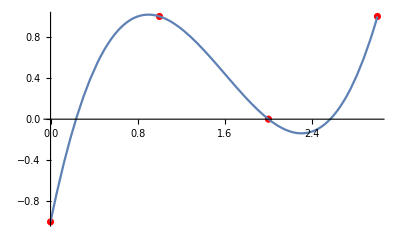

```mathematica
data={{0,-1},{1,1},{2,0},{3,1}};
(*data=Table[{i-1,Random[]},{i,3}]*)
polynomial=Fit[data,Table[x^i,{i,0,Length[data]-1}],x]
hoc[data]
Show[ListPlot[data,PlotStyle->Red],Plot[polynomial,{x,0,data[[-1,1]]}]]
```

```mathematica
(*highest order coefficient*)
hoc[data_]:=With[{s=Flatten[Take[#,-1]&/@data],n=Length[data]-1},1/Factorial[n]*Sum[(-1)^(n+i)*Binomial[n,i]*s[[i+1]],{i,0,n}]]
out[data_]:=With[{s=Flatten[Take[#,-1]&/@data],n=Length[data]-1,q=.04},-s⟦1⟧+4 s⟦2⟧-6 s⟦3⟧+4 s⟦4⟧-24 *q]
out[data]
```

8.04

```mathematica
Clear[a,b,c,d,s,q,data,n];
```

```mathematica
Solve[3*q+1/2*(a-2b+c)==1/2*(b-2 c+d),d]
```

{{d→a-3 b+3 c+6 q}}

```mathematica
data={{0,-3},{1,0},{2,0},{3,3}};
s=Flatten[Take[#,-1]&/@data];
n=Length[data]-1;
q = 1/2;
data[[-1,2]]=s⟦1⟧-3 s⟦2⟧+3 s⟦3⟧-6q;
Print["s[[-1]] = ",data[[-1,2]]]
Print["calculated hoc = ",hoc[data]]
```

s[[-1]] = -6

calculated hoc = -1/2

```mathematica
hoc[{{0,-3},{1,0},{2,0},{3,-3}}]
```

0

```mathematica
data[[-1,2]]=2
data
```

2

{{0,1},{1,0},{2,1},{3,2}}

```mathematica
(*Solution Formula*)
n=3;
Sum[(-1)^(n+i+1)*Binomial[n,i]*s[[i+1]],{i,0,n-1}]+Factorial[n]*q
```

Part::partd: Part specification s⟦1⟧ is longer than depth of object.

Part::partd: Part specification s⟦2⟧ is longer than depth of object.

Part::partd: Part specification s⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

6 q+s⟦1⟧-3 s⟦2⟧+3 s⟦3⟧